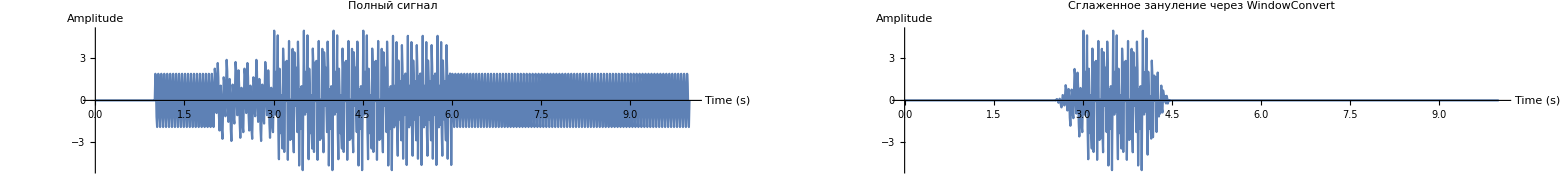

```mathematica
spec=<|MaxTime->10,SampleRate->100,Components->{<|Amplitude->2,Frequency->20,TStart->1,TEnd->10|>,<|Amplitude->3,Frequency->32,TStart->3,TEnd->6|>,<|Amplitude->1,Frequency->6,TStart->2,TEnd->5|>}|>;

data=Table[{t,Total@Map[If[#[TStart]<=t<=#[TEnd],1,0]*#[Amplitude]*Sin[2 Pi t #[Frequency]]&,spec[Components]]},{t,0,spec[MaxTime],1/spec[SampleRate]}];

(* Оконная функция (сглаженная)*)
smoothMask[t_,tStart_,tEnd_,edge_]:=Module[{rampUp,rampDown},rampUp=0.5*(1+Cos[Pi*(tStart+edge-t)/edge]);
rampDown=0.5*(1+Cos[Pi*(t-tEnd+edge)/edge]);
Which[t<=tStart,0,t<tStart+edge,rampUp,t<=tEnd-edge,1,t<=tEnd,rampDown,True,0]];


WindowConvert[data_,windowFunc_,tStart_,tEnd_,opts___]:=Map[{#[[1]],windowFunc[#[[1]],tStart,tEnd,opts]*#[[2]]}&,data];


cut=<|Start->2.5,End->4.5,Edge->0.5|>;

smoothSignal=WindowConvert[data,smoothMask,cut[Start],cut[End],cut[Edge]];


p1=ListLinePlot[data,PlotRange->All,PlotLabel->"Полный сигнал",AspectRatio->1/5,ImageSize->1000,AxesLabel->{"Time (s)","Amplitude"}];

p2=ListLinePlot[smoothSignal,PlotRange->All,PlotLabel->"Сглаженное зануление через WindowConvert",AspectRatio->1/5,ImageSize->1000,AxesLabel->{"Time (s)","Amplitude"}];

GraphicsRow[{p1,p2}]
```

```mathematica
{freqs,times,spectro}=WindowSpectrogram[smoothSignal[[All,2]],spec[SampleRate],128,16];

ListPlot3D[spectro,DataRange->{{times[[1]],times[[-1]]},{freqs[[1]],freqs[[-1]]}},AxesLabel->{"Time (s)","Frequency (Hz)","Amplitude"},ColorFunction->"SunsetColors",Mesh->None,PlotLabel->"3D спектрограмма сглаженного сигнала"]
```

-Graphics3D-

```mathematica
{freqsFull,timesFull,spectroFull}=WindowSpectrogram[data[[All,2]],spec[SampleRate],128,16];

ListPlot3D[spectroFull,DataRange->{{timesFull[[1]],timesFull[[-1]]},{freqsFull[[1]],freqsFull[[-1]]}},AxesLabel->{"Time (s)","Frequency (Hz)","Amplitude"},ColorFunction->"SunsetColors",Mesh->None,PlotLabel->"3D спектрограмма полного сигнала"]
```

-Graphics3D-